```mathematica
UnitForm[units_][quantity_]:=UnitConvert[quantity,units]
```

### Constants

```mathematica
filters={"Blue","Yellow","Red","NoFilter"};
colorFilters=filters[[;;3]];
colorWavelengths=Quantity[{4495,5490,6500},"Angstroms"];
color=<|"NoFilter"->(Gray&),"Red"->(Red&),"Blue"->(Blue&),"Yellow"->(Green&)|>;
samples={"White","BK7","SF58"};
sampleThickness=Quantity[{1.036,0.956,1.272},"cm"];
magnetism={5,-90,-166,-259,-5,83,167,243};
```

### Malus Law

```mathematica
FitMalusFull[filter_]:=
Module[{rawData,n,chunks,μ,σ,around,angles},
rawData=Rest[Import[NotebookDirectory[]<>"Malus"<>filter<>".xlsx","XLSX"][[1]]]ᵀ[[2]];
n=Length@rawData/10-1;
{μ,σ}=Table[#@rawData[[10i+1;;10i+10]]&/@{Mean,StandardDeviation},{i,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
angles=Range[0,10n+1,10]°;
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
Print[fit];
Print[fit["ParameterTable"]];
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,0,angles[[-1]]},ColorFunction->color[filter]]
]
]
```

FittedModel[-0.0015013-0.0385886 Cos[1.10467-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.0015013 | 0.000017872 | -84.0031 | 5.10037×10^-41
m_2 | 0.0385886 | 0.0000206507 | 1868.63 | 8.63509×10^-87
m_3 | 1.10467 | 0.00049499 | 2231.71 | 2.06263×10^-89

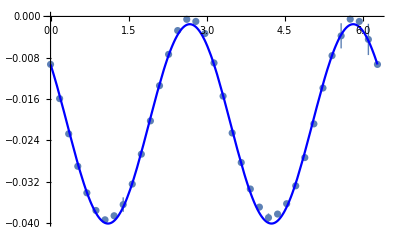

```mathematica
FitMalusFull["Blue"]
```

```mathematica
FitMalusFull[filters[[1]]]
```

FittedModel[-0.0015013-0.0385886 Cos[1.10467-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.0015013 | 0.000017872 | -84.0031 | 5.10037×10^-41
m_2 | 0.0385886 | 0.0000206507 | 1868.63 | 8.63509×10^-87
m_3 | 1.10467 | 0.00049499 | 2231.71 | 2.06263×10^-89

-Graphics-

FittedModel[-0.00061743-0.0390204 Cos[1.10733-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.00061743 | 6.10432×10^-6 | -101.146 | 9.46303×10^-44
m_2 | 0.0390204 | 0.0000179432 | 2174.67 | 4.97455×10^-89
m_3 | 1.10733 | 0.000241489 | 4585.45 | 4.79912×10^-100

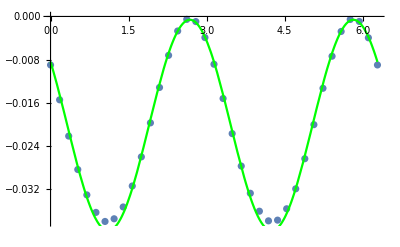

```mathematica
FitMalusFull[filters[[2]]]
```

```mathematica
field[i_]:=magnetism[[Floor[i/9]+1]];
sample[i_]:=samples[[Mod[Floor[i/3],3]+1]];
filter[i_]:=colorFilters[[Mod[i,3]+1]];
startAngles=Table@@@{{195, 9}, {190, 2}, {195, 4}, {200, 3}, {180, 1}, {190, 2}, {200, 1}, {195, 2}, {200, 3}, {175, 1}, {185, 1}, {190, 1}, {200, 1}, {195, 1}, {200, 4}, {195, 1}, {200, 5}, {195, 3}, {200, 9}, {210, 3}, {200, 3}, {195, 2}, {200, 1}, {220, 1}, {215, 2}, {195, 1}, {205, 1}, {190, 2}, {195, 2}}//Flatten;
```

```mathematica
Table[{i,field@i,sample@i,filter@i,startAngles[[i+1]]},{i,0,8*9-1}]//TableForm
```

0 | 5 | White | Blue | 195
1 | 5 | White | Yellow | 195
2 | 5 | White | Red | 195
3 | 5 | BK7 | Blue | 195
4 | 5 | BK7 | Yellow | 195
5 | 5 | BK7 | Red | 195
6 | 5 | SF58 | Blue | 195
7 | 5 | SF58 | Yellow | 195
8 | 5 | SF58 | Red | 195
9 | -90 | White | Blue | 190
10 | -90 | White | Yellow | 190
11 | -90 | White | Red | 195
12 | -90 | BK7 | Blue | 195
13 | -90 | BK7 | Yellow | 195
14 | -90 | BK7 | Red | 195
15 | -90 | SF58 | Blue | 200
16 | -90 | SF58 | Yellow | 200
17 | -90 | SF58 | Red | 200
18 | -166 | White | Blue | 180
19 | -166 | White | Yellow | 190
20 | -166 | White | Red | 190
21 | -166 | BK7 | Blue | 200
22 | -166 | BK7 | Yellow | 195
23 | -166 | BK7 | Red | 195
24 | -166 | SF58 | Blue | 200
25 | -166 | SF58 | Yellow | 200
26 | -166 | SF58 | Red | 200
27 | -259 | White | Blue | 175
28 | -259 | White | Yellow | 185
29 | -259 | White | Red | 190
30 | -259 | BK7 | Blue | 200
31 | -259 | BK7 | Yellow | 195
32 | -259 | BK7 | Red | 200
33 | -259 | SF58 | Blue | 200
34 | -259 | SF58 | Yellow | 200
35 | -259 | SF58 | Red | 200
36 | -5 | White | Blue | 195
37 | -5 | White | Yellow | 200
38 | -5 | White | Red | 200
39 | -5 | BK7 | Blue | 200
40 | -5 | BK7 | Yellow | 200
41 | -5 | BK7 | Red | 200
42 | -5 | SF58 | Blue | 195
43 | -5 | SF58 | Yellow | 195
44 | -5 | SF58 | Red | 195
45 | 83 | White | Blue | 200
46 | 83 | White | Yellow | 200
47 | 83 | White | Red | 200
48 | 83 | BK7 | Blue | 200
49 | 83 | BK7 | Yellow | 200
50 | 83 | BK7 | Red | 200
51 | 83 | SF58 | Blue | 200
52 | 83 | SF58 | Yellow | 200
53 | 83 | SF58 | Red | 200
54 | 167 | White | Blue | 210
55 | 167 | White | Yellow | 210
56 | 167 | White | Red | 210
57 | 167 | BK7 | Blue | 200
58 | 167 | BK7 | Yellow | 200
59 | 167 | BK7 | Red | 200
60 | 167 | SF58 | Blue | 195
61 | 167 | SF58 | Yellow | 195
62 | 167 | SF58 | Red | 200
63 | 243 | White | Blue | 220
64 | 243 | White | Yellow | 215
65 | 243 | White | Red | 215
66 | 243 | BK7 | Blue | 195
67 | 243 | BK7 | Yellow | 205
68 | 243 | BK7 | Red | 190
69 | 243 | SF58 | Blue | 190
70 | 243 | SF58 | Yellow | 195
71 | 243 | SF58 | Red | 195

```mathematica
ClearAll@FitFaradata
geti[field_,sample_,filter_]:=3^2(Position[magnetism,field][[1,1]]-1)+3(Position[samples,sample][[1,1]]-1)+Position[colorFilters,filter][[1,1]]-1;
(*FitFaradata[field_,sample_,filter_,opts:OptionsPattern[{plot->False,params->False}]]:=FitFaradata[
3^2(Position[magnetism,field][[1,1]]-1)+3(Position[samples,sample][[1,1]]-1)+Position[colorFilters,filter][[1,1]]-1,
opts
];*)
(*FitFaradata[i_,opts:OptionsPattern[{plot->False,params->False}]]:=*)
FitFaradata[field_,sample_,filter_,opts:OptionsPattern[{plot->False,params->False}]]:=Module[
{
angleStart=startAngle[geti[field,sample,filter]],
rawData,n,chunks,μ,σ,around,angles
},
Print[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx"];
rawData=Rest[Import[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx","XLSX"][[1]]]ᵀ[[2]];
startAngle=startAngles[[0+1]];
n=Length@rawData/10-1;
{angles,μ,σ}=Table[Join[{startAngle-10j}°,#@rawData[[10j+1;;10j+10]]&/@{Mean,StandardDeviation}],{j,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
(*Print[fit];*)
If[OptionValue[params],
Print[fit["ParameterTable"]]
];
If[OptionValue[plot],
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,angles[[1]],angles[[-1]]},ColorFunction->color[filter]]
]
];
fit
]
```

```mathematica
Table[Subscript[m, 3]/.FitFaradata[field,"White","Blue"]["BestFitParameters"],{field,magnetism}]
```

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\5WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\-90WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\-166WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\-259WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\-5WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\83WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\167WhiteBlueMin.xlsx

C:\Users\andre\Documents\Rutgers\S23\388\Faraday Lab\243WhiteBlueMin.xlsx

{1.10421,1.06093,1.09471,1.0938,1.10421,1.14168,1.09405,1.03734}

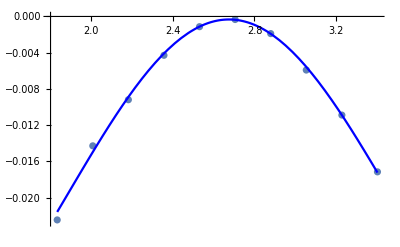

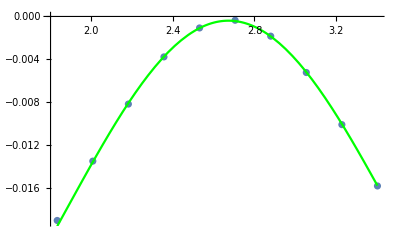

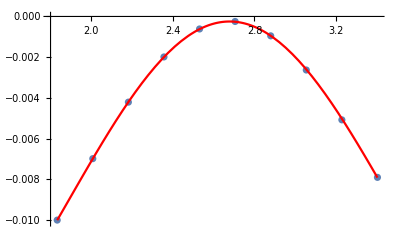

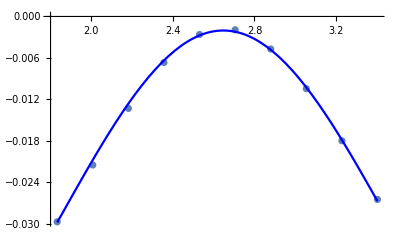

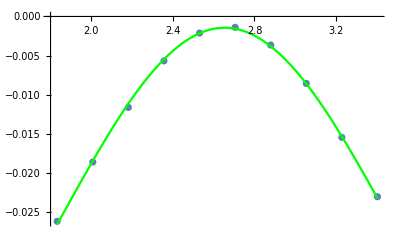

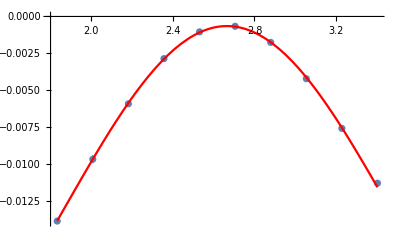

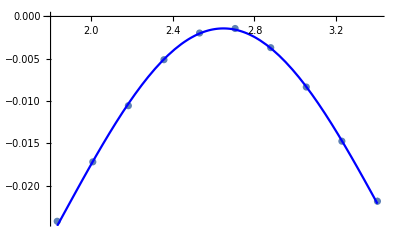

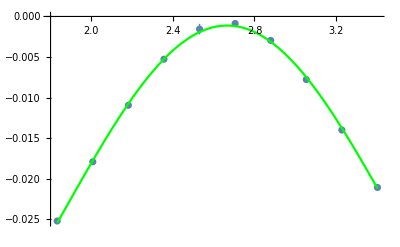

{2.67501,2.67276,2.67814,2.64735,2.65343,2.66513,2.64772,2.66598,2.66859,2.63173,2.68075,2.61124,2.65686,2.66347,2.66851,2.63004,2.61936,2.60146,2.6655,2.59661,2.63988,2.57496,2.66678,2.66963,2.67847,2.65252,2.62542,2.6646,2.61334,2.59496,2.58493,2.66818,2.59207,2.74191,2.67648,2.65009}

```mathematica
Table[θ/.FindMaximum[FitFaradata[j,plot->True]//Normal,{θ,2.7}][[2]],{j,0,35}]
```

```mathematica
s
```